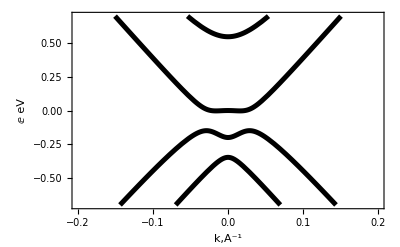

```mathematica
tp=0.4; d1=0.05; d2=-0.15; U=-0.15; c=6.25;
A1=U^2+(d1^2+d2^2)/2+tp^2/2;
A3=U^4-U^2*(d1^2+d2^2)+d1^2*d2^2+tp^2*(U^2-U*(d1+d2)+d1*d2);
A7=2*U^2-d1^2-d2^2;
a[x_]=2*((c*x)^2+A1);
b=2*(U*(d1^2-d2^2)+tp^2*(d1-d2)/2);
ch[x_]=4*(A3-A7*(c*x)^2+(c*x)^4);
dh[x_]=a[x]*ch[x]+b^2;
s[x_]=-a[x]^2/3-ch[x];
qh[x_]=(2*a[x]^3/27+(a[x]*ch[x])/3-dh[x]);
Q1[x_]=((qh[x]^2)/4+(s[x]^3)/27);
Q[x_]=Sqrt[Q1[x]];
Qh[x_]=-qh[x]/2+Q[x];
K1[x_]=Qh[x]^(1/3);
Wh[x_]=qh[x]/2+Q[x];
K2[x_]=Wh[x]^(1/3);
K[x_]=K1[x]-K2[x];
Y[x_]=(-qh[x]/2+Q[x])^(1/3)+(-qh[x]/2-Q[x])^(1/3);
r[x_]=Y[x]-a[x]/3;
f[x_]=Sqrt[(r[x]+a[x])];  
g[x_]=(b+r[x]*f[x])/(2*f[x]);
G[x_]=(b-r[x]*f[x])/(2*f[x]);
f1[x_]=(-f[x]+(f[x]^2-4*g[x])^(1/2))/2;  
f2[x_]=(-f[x]-(f[x]^2-4*g[x])^(1/2))/2;
f3[x_]=(f[x]+(f[x]^2+4*G[x])^(1/2))/2;
 f4[x_]=(f[x]-(f[x]^2+4*G[x])^(1/2))/2;   
Plot[{f1[x],f2[x],f3[x],f4[x]},{x,-0.2,0.2},AxesLabel->{"k,A^-1",E eV},PlotRange->{-0.7,0.7},PlotStyle->{{Thickness[0.009],Black},{Thickness[0.009],Black},{Thickness[0.009],Black},{Thickness[0.009],Black}},Frame->True]
```

```mathematica
Export["A5.pdf",Plot[{f1[x],f2[x],f3[x],f4[x]},{x,-0.2,0.2},AxesLabel->{"k,A^-1",E eV},PlotRange->{-0.7,0.7},PlotStyle->{{Thickness[0.003],Black},{Thickness[0.003],Black},{Thickness[0.003],Black},{Thickness[0.003],Black}},Frame->True]]
```

A5.pdf

```mathematica
"A3.pdf"
```

A3.pdf